```mathematica
<<NounouW`
```

HokahokaW`
Git HEAD hash loaded on Mon 6 Apr 2015 17:15:50 is dfc276416b3fda60a30e53692c8c82eaed59709c.
Remember that this is at latest the penultimate commit before deployment. You should use a live git repo if possible, for better version tracking.

NounouW`
Git HEAD hash loaded on Mon 6 Apr 2015 19:49:18 is a7b569f93d24f934eedde6a6ac130f15f8bd31fe.
Remember that this is at latest the penultimate commit before deployment. You should use a live git repo if possible, for better version tracking.

```mathematica
AllowRaggedArrays[True]
```

```mathematica
layout =JavaNew["nounou.elements.layouts.NNDataLayoutHexagonal", {{-1, 15,14,13,12,11}, {10, 9, 8, 1, 0}, {7, 6, 5, 4}, {-1, 3,2}}]
```

«JavaObject[nounou.elements.layouts.NNDataLayoutHexagonal]»

```mathematica
(layout@mask[#])& /@ {2,4};
```

```mathematica
layout@toJsonString[]
```

{"layoutArray":[[-1,15,14,13,12,11],[10,9,8,1,0],[7,6,5,4],[-1,3,2]],"channelRadius":50.0,"channelDistance":100.0,"masked":[2,4],"className":"nounou.elements.layouts.NNDataLayoutHexagonal","gitHead":"674199eda7404048d811c228fb848bd74709fd6a","version":0.5,"bitmap$0":false}

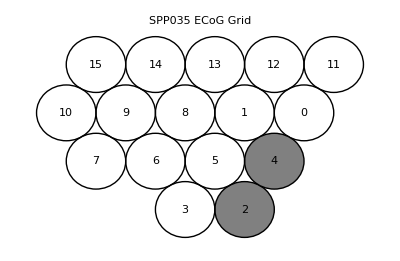

```mathematica
NNDetectorPlot[layout, PlotLabel-> "SPP035 ECoG Grid"]
```